```mathematica
GammaConnection[coord_List,Metric_List]:=Block[{n,InverseMetric,t,ChristoffelSymbols,listChristoffelSymbols,iind,jind,kind,lind,gamma,racciM},
n=Length[coord];
InverseMetric=Simplify[Inverse[Metric]];
ChristoffelSymbols=Table[1/2*Sum[(InverseMetric[[kind,lind]])*(D[Metric[[jind,lind]],coord[[iind]]]+D[Metric[[iind,lind]],coord[[jind]]]-D[Metric[[iind,jind]],coord[[lind]]]),{lind,1,n}],{kind,1,n},{iind,1,n},{jind,1,n}]
]
Racci[gamma_,mu_,sig_,co_]:=Sum[D[gamma[nu,mu,sig],co[[nu]]],{nu,1,Length[co]}]-Sum[D[gamma[nu,nu,sig],co[[mu]]],{nu,1,Length[co]}]+Sum[gamma[la,mu,sig]gamma[nu,la,nu],{nu,1,Length[co]},{la,1,Length[co]}]-Sum[gamma[la,nu,sig]gamma[nu,la,mu],{nu,1,Length[co]},{la,1,Length[co]}]
racciCurFromMetric[coord_List,Metric_List]:=Block[{n,InverseMetric,t,ChristoffelSymbols,listChristoffelSymbols,iind,jind,kind,lind,gamma,racciM},
n=Length[coord];
InverseMetric=Simplify[Inverse[Metric]];
ChristoffelSymbols=GammaConnection[coord,Metric];
Do[gamma[kind,iind,jind]=ChristoffelSymbols[[kind,iind,jind]],{kind,1,n},{iind,1,n},{jind,1,n}];
racciM=Table[Racci[gamma,mu,sig,coord],{mu,1,n},{sig,1,n}];
racciM
]
(*Subscript[R, abc]^d*)
riemannTensorFromMetric[coord_List,Metric_List]:=Block[{n,InverseMetric,t,ChristoffelSymbols,iind,jind,kind,lind,inda,indb,indc,indd,riemann},
n=Length[coord];
InverseMetric=Simplify[Inverse[Metric]];
ChristoffelSymbols=Simplify[Table[1/2*Sum[(InverseMetric[[kind,lind]])*(D[Metric[[jind,lind]],coord[[iind]]]+D[Metric[[iind,lind]],coord[[jind]]]-D[Metric[[iind,jind]],coord[[lind]]]),{lind,1,n}],{kind,1,n},{iind,1,n},{jind,1,n}]];
riemann=Table[-D[ChristoffelSymbols[[indd,indb,indc]],coord[[inda]]]+D[ChristoffelSymbols[[indd,inda,indc]],coord[[indb]]]+Sum[
ChristoffelSymbols[[inde,indc,inda]]ChristoffelSymbols[[indd,indb,inde]],{inde,1,n} ]-Sum[
ChristoffelSymbols[[inde,indc,indb]]ChristoffelSymbols[[indd,inda,inde]],{inde,1,n} ],{inda,1,n},{indb,1,n},{indc,1,n},{indd,1,n}
]
]
extrinsicCur[gmetric_,coorList_,conormal_,spaceTimeLike_]:=Block[{ginv,christoffelSymbols,normalizedConorm,h3metric,projection,extrinsicK},
ginv=Inverse[gmetric];
christoffelSymbols=GammaConnection[coorList,gmetric];
normalizedConorm=conormal/√(spaceTimeLike conormal.ginv.conormal);
h3metric=gmetric-spaceTimeLike TensorProduct[normalizedConorm,normalizedConorm];
projection=h3metric.ginv;
extrinsicK=projection.(D[normalizedConorm,{coorList}]-normalizedConorm.christoffelSymbols).Transpose[projection]
]
funD[f_,k_[x_]]:=Block[{order},
order=Cases[f,Derivative[_][k][x],Infinity]//DeleteDuplicates;
order=order/.Derivative[n_][k][x]:>n;
D[f,k[x]]+Total[Map[(-1)^# D[D[f,Derivative[#][k][x]],{x,#}]&,order]]
]
(*canonicalPairs should be {{{x1,p1},(the valur of [x1,p1])},...}*)
poissonFun[{f1_,f2_},canonicalPairs_]:=(#[[2]](funD[f1,#[[1,1]]]funD[f2,#[[1,2]]]-funD[f2,#[[1,1]]]funD[f1,#[[1,2]]])&/@canonicalPairs)//Total
lieDerivative[vector_,tensor_,type_,coor_]/;type=={0,0}:=D[tensor,{coor}].vector
(*here a tensor with the type (m,n) should be input as tensor[[a1,a2,...,am,b1,...,bn]]*)
lieDerivative[vector_,tensor_,type_,coor_]/;type=!={0,0}:=Block[{term1,term2,term3,contractingIndex,resortIndex},
term1=D[tensor,{coor}].vector;
contractingIndex=Insert[Range[2,Total[type]],1,#]&/@Range[Total[type]];
resortIndex=TakeDrop[Range[Total[type]],{#}]&/@Range[Total[type]];
resortIndex=Flatten/@resortIndex;
term2=If[type[[1]]==0,0,(D[vector,{coor}].Transpose[tensor,#])&/@contractingIndex[[Range[type[[1]]]]]];
term2=If[type[[1]]==0,0,MapThread[Transpose[#1,#2]&,{term2,resortIndex[[Range[type[[1]]]]]}]];
term2=-term2//Total;
term3=If[type[[2]]==0,0,(Transpose[D[vector,{coor}]].Transpose[tensor,#])&/@contractingIndex[[Range[type[[1]]+1,Total[type]] ]]];
term3=If[type[[2]]==0,0,MapThread[Transpose[#1,#2]&,{term3,resortIndex[[ Range[type[[1]]+1,Total[type]] ]]}]];
term3=term3//Total;
term1+term2+term3
]
findScalars[variablesWithWeight_]:=Block[{variablesWithWeightp,allVariables,density1pairs,newScalars},
variablesWithWeightp=If[#[[2]]==0,{#,D[#[[1]],x]->1},#]&/@variablesWithWeight//Flatten;
allVariables=Reverse/@variablesWithWeightp;
allVariables=GroupBy[allVariables,Keys,Last/@#&];
density1pairs=Subsets[allVariables[1],{2}];
density1pairs=DeleteCases[density1pairs,_?(AllTrue[#, MemberQ[#,Derivative,Infinity,Heads->True]&]&)];
density1pairs=SortBy[#,!MemberQ[#,Derivative,Infinity,Heads->True]&]&/@density1pairs;
newScalars=#[[1]]/#[[2]]&/@density1pairs;
newScalars=newScalars->0//Thread;
{variablesWithWeightp,newScalars}//DeleteDuplicates//Flatten
]
```

```mathematica
HvGau=-(K1[x] E1'[x]-2 E2[x] K2'[x])/(2 G);
HScal=(-8 E1[x] E2[x]^2 K1[x] K2[x]-4 E2[x]^3 (1+K2[x]^2)-4 E1[x] E1'[x] E2'[x]+E2[x] (E1'[x]^2+4 E1[x] E1''[x]))/(8 G √E1[x] E2[x]^2);
```

```mathematica
arealGF1=E1->Function[x,x^2];
arealGF2=Solve[0==HvGau/.arealGF1,K1[x]]//First;
arealGF2=K1->Function[x,Evaluate[K1[x]/.arealGF2]];
arealGF={arealGF1,arealGF2}//Flatten
```

{E1→Function[x,x^2],K1→Function[x,(E2[x] K2'[x])/x]}

```mathematica
canonicalPairs={{{K1[x],E1[x]},2G},{{K2[x],E2[x]},G}};
```

```mathematica
allVariables={E1[x],E2[x],K1[x],K2[x]};
allVariables=allVariables->{0,1,1,0}//Thread
```

{E1[x]→0,E2[x]→1,K1[x]→1,K2[x]→0}

```mathematica
allScalars=Nest[findScalars,allVariables,3];
allScalars=GroupBy[allScalars,Values,Keys];
allScalars=allScalars[0]//FullSimplify//DeleteDuplicates;
allScalars=DeleteCases[allScalars,_?(MemberQ[#,Derivative[_][f_][x]/;MemberQ[{K1,K2},f],Infinity]&)];
allScalars=DeleteCases[allScalars,_?(MemberQ[#,Derivative[n_][_][x]/;n≥3,Infinity]&)];
allScalars=allScalars/.E2[x]/K1[x]->K1[x]/E2[x];
allScalars=allScalars->{1,2,4,5,3,6,7}//Thread;
allScalars=SortBy[allScalars,Last]//Keys;
```

```mathematica
Hv1=Nx[x]HvGau;
```

```mathematica
poissonHvScalars=Expand[poissonFun[{Smear[x]#,Hv1},canonicalPairs]]&/@allScalars;
poissonHvScalars=poissonHvScalars+(D[Nx[x]Smear[x],x]allScalars)//Expand;
poissonHvScalars=Integrate[#,x]&/@poissonHvScalars;
AllTrue[Head/@poissonHvScalars,#=!=Integrate&]
```

True

```mathematica
selfPoisson={N1[x]#,N2[x]#}&/@allScalars;
selfPoisson=poissonFun[{#[[1]],#[[2]]},canonicalPairs]&/@selfPoisson//Expand;
selfPoisson=selfPoisson/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>-D[Times[a],x]D[f[x],x]//Expand;
selfPoissonByNpN=selfPoisson/(N2[x] N1'[x]-N1[x] N2'[x])//Simplify//Expand
```

{0,0,0,0,-(2 G E1'[x])/K1[x]^3,0,-(4 G E1'[x] E2'[x]^2)/(E2[x]^4 K1[x]^3)-(2 G E1'[x] E2'[x] K1'[x])/(E2[x]^3 K1[x]^4)+(4 G E2'[x] E1''[x])/(E2[x]^3 K1[x]^3)+(2 G K1'[x] E1''[x])/(E2[x]^2 K1[x]^4)+(2 G E1'[x] E2''[x])/(E2[x]^3 K1[x]^3)-(2 G E1^(3)[x])/(E2[x]^2 K1[x]^3)}

```mathematica
scalar8=1/E2[x] D[allScalars[[-2]],x]//Simplify;
p1=poissonFun[{N1[x]scalar8,N2[x]allScalars[[3]]},canonicalPairs]//Expand
p2=poissonFun[{N2[x]scalar8,N1[x]allScalars[[3]]},canonicalPairs]//Expand
p1-p2/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand
%/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand
```

-(30 G N1[x] N2[x] E2'[x]^3)/E2[x]^7+(30 G N2[x] E2'[x]^2 N1'[x])/E2[x]^6+(20 G N1[x] N2[x] E2'[x] E2''[x])/E2[x]^6-(8 G N2[x] N1'[x] E2''[x])/E2[x]^5-(12 G N2[x] E2'[x] N1''[x])/E2[x]^5-(2 G N1[x] N2[x] E2^(3)[x])/E2[x]^5+(2 G N2[x] N1^(3)[x])/E2[x]^4

-(30 G N1[x] N2[x] E2'[x]^3)/E2[x]^7+(30 G N1[x] E2'[x]^2 N2'[x])/E2[x]^6+(20 G N1[x] N2[x] E2'[x] E2''[x])/E2[x]^6-(8 G N1[x] N2'[x] E2''[x])/E2[x]^5-(12 G N1[x] E2'[x] N2''[x])/E2[x]^5-(2 G N1[x] N2[x] E2^(3)[x])/E2[x]^5+(2 G N1[x] N2^(3)[x])/E2[x]^4

(10 G N2[x] E2'[x]^2 N1'[x])/E2[x]^6-(10 G N1[x] E2'[x]^2 N2'[x])/E2[x]^6-(4 G N2[x] N1'[x] E2''[x])/E2[x]^5+(4 G N1[x] N2'[x] E2''[x])/E2[x]^5-(2 G N2'[x] N1''[x])/E2[x]^4+(2 G N1'[x] N2''[x])/E2[x]^4

(10 G N2[x] E2'[x]^2 N1'[x])/E2[x]^6-(10 G N1[x] E2'[x]^2 N2'[x])/E2[x]^6-(4 G N2[x] N1'[x] E2''[x])/E2[x]^5+(4 G N1[x] N2'[x] E2''[x])/E2[x]^5-(2 G N2'[x] N1''[x])/E2[x]^4+(2 G N1'[x] N2''[x])/E2[x]^4

```mathematica
selfPoissonTerms=poissonFun[{N1[x]E2[x]F[Other[x],allScalars[[7]]],N2[x]E2[x]F[Other[x],allScalars[[7]]]},canonicalPairs]//Expand;
selfPoissonTerms=selfPoissonTerms/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>-D[Times[a],x]D[f[x],x]//Expand;
selfPoissonTerms=selfPoissonTerms/(2 G (N1[x] N2'[x]-N2[x] N1'[x]))//Simplify//Expand;
selfPoissonTerms==1/K1[x]^2 E2[x]D[allScalars[[7]],x](Derivative[0,1][F][Other[x],(-E1'[x] E2'[x]+E2[x] E1''[x])/(E2[x]^2 K1[x])])^2//Expand
```

True

```mathematica
selfPoissonTerms=poissonFun[{N1[x]E2[x]F[allScalars[[5]],Other[x]],N2[x]E2[x]F[allScalars[[5]],Other[x]]},canonicalPairs]//Simplify;
selfPoissonTerms=selfPoissonTerms/(2 G (N1[x] N2'[x]-N2[x] N1'[x]))//Simplify//Expand
selfPoissonTerms==(E2[x]^2 allScalars[[5]])/K1[x]^2(Derivative[1,0][F][allScalars[[5]],Other[x]])^2
```

(E2[x]^2 E1'[x] (F^(1,0)[E1'[x]/K1[x],Other[x]])^2)/K1[x]^3

True

```mathematica
scalarPairs1=Table[{N1[x]extraTerm[a,x]allScalars[[a]],N2[x]extraTerm[b,x]allScalars[[b]]},{a,1,7},{b,1,7}];
poissonPair1=Map[poissonFun[{#[[1]],#[[2]]},canonicalPairs]&,scalarPairs1,{2}]//Simplify;
Print["terms not propotional to delta(x,y)"]
Sort/@Position[poissonPair1,HoldPattern[Times[___,N1[x],___,N2[x],___]|0],{2}]//DeleteDuplicates//DeleteCases[#,{i_,i_}]&
scalarPairs2=Table[{N2[x]extraTerm[a,x]allScalars[[a]],N1[x]extraTerm[b,x]allScalars[[b]]},{a,1,7},{b,1,7}];
poissonPair2=Map[poissonFun[{#[[1]],#[[2]]},canonicalPairs]&,scalarPairs2,{2}]//Expand;
poissonPair=poissonPair1-poissonPair2//Expand;
(poissonPair=ReplacePart[poissonPair,{i_,i_}:>0]//FullSimplify//Expand)//MatrixForm;
poissonPair=poissonPair/.Times[a___,Derivative[2][f_][x]/;MemberQ[{N1,N2},f]]:>-D[Times[a],x]D[f[x],x];
poissonPair=poissonPair/.extraTerm:>Function[{a,x},E2[x]Derivative[0,1][F][other[x],s[a,x]]];
(poissonPair=poissonPair/(2 G (N1[x] N2'[x]-N2[x] N1'[x]))//Simplify);
vanishingTerms=Sort/@DeleteCases[Position[poissonPair,0,{2}],{i_,i_}]//DeleteDuplicates
nonVanishingTerms=Sort/@Position[poissonPair,_?(#=!=0&),{2},Heads->False]//DeleteDuplicates
DeleteCases[nonVanishingTerms,{_,5|7}|{5|7,_}]
```

terms not propotional to delta(x,y)

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{4,6}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{4,6}}

{{2,6},{2,7},{3,4},{3,5},{3,6},{3,7},{4,5},{4,7},{5,6},{5,7},{6,7}}

{{2,6},{3,4},{3,6}}

```mathematica
poissonPair[[2,6]]
poissonPair[[2,7]]
poissonPair[[3,4]]
poissonPair[[3,5]]
```

(E1'[x] F^(0,1)[other[x],s[2,x]] F^(0,1)[other[x],s[6,x]])/(2 E2[x])

(E1'[x] F^(0,1)[other[x],s[2,x]] F^(0,1)[other[x],s[7,x]])/(2 K1[x])

-F^(0,1)[other[x],s[3,x]] F^(0,1)[other[x],s[4,x]]

-(E2[x] F^(0,1)[other[x],s[3,x]] F^(0,1)[other[x],s[5,x]])/K1[x]

```mathematica
poissonPair[[3,6]]==1/E2[x](Derivative[0,1][F][other[x],s[3,x]]D[Derivative[0,1][F][other[x],s[6,x]],x]-D[Derivative[0,1][F][other[x],s[3,x]],x]Derivative[0,1][F][other[x],s[6,x]])
```

True

```mathematica
poissonPair[[3,7]]==Derivative[0,1][F][other[x],s[3,x]] D[(Derivative[0,1][F][other[x],s[7,x]])/K1[x],x]-(E2[x]Derivative[0,1][F][other[x],s[7,x]])/K1[x] D[1/E2[x] Derivative[0,1][F][other[x],s[3,x]],x]//Expand
```

True

```mathematica
poissonPair[[4,5]]
```

(E2[x] E1'[x] F^(0,1)[other[x],s[4,x]] F^(0,1)[other[x],s[5,x]])/K1[x]^2

```mathematica
poissonPair[[4,7]]==Derivative[0,1][F][other[x],s[4,x]]Derivative[0,1][F][other[x],s[7,x]]D[D[E1[x],x]/E2[x],x] E2[x]/K1[x]^2//Expand
```

True

```mathematica
poissonPair[[5,6]]==(Derivative[0,1][F][other[x],s[5,x]] Derivative[0,1][F][other[x],s[6,x]]D[D[E1[x],x]/K1[x]^2,x]-(E2[x]D[E1[x],x])/K1[x]^2 Derivative[0,1][F][other[x],s[5,x]]D[1/E2[x] Derivative[0,1][F][other[x],s[6,x]],x]+E1'[x]/K1[x]^2 Derivative[0,1][F][other[x],s[6,x]]D[Derivative[0,1][F][other[x],s[5,x]],x])//Expand
```

True

```mathematica
poissonPair[[5,7]]==(Derivative[0,1][F][other[x],s[5,x]]Derivative[0,1][F][other[x],s[7,x]] E2[x]/K1[x]^2 D[D[E1[x],x]/K1[x],x]+(E2[x] Derivative[0,1][F][other[x],s[7,x]])/K1[x]^2 D[D[E1[x],x]/K1[x] Derivative[0,1][F][other[x],s[5,x]],x]-(E1'[x] Derivative[0,1][F][other[x],s[5,x]])/K1[x]^2 D[E2[x]/K1[x] Derivative[0,1][F][other[x],s[7,x]],x])//Expand
```

True

```mathematica
poissonPair[[6,7]]==(Derivative[0,1][F][other[x],s[6,x]] Derivative[0,1][F][other[x],s[7,x]] 1/E2[x] D[(E2[x]E1''[x]-E2'[x]E1'[x])/(E2[x] K1[x]^2),x]+Derivative[0,1][F][other[x],s[7,x]](E1'[x] E2'[x]-E1''[x] E2[x])/(K1[x]^2 E2[x]^2)D[ Derivative[0,1][F][other[x],s[6,x]],x]-(E1'[x] E2'[x]-E1''[x]E2[x])/(E2[x]^2 K1[x]^2) Derivative[0,1][F][other[x],s[6,x]]D[ Derivative[0,1][F][other[x],s[7,x]],x])//Expand
```

True

```mathematica
allScalars4H=Most[allScalars]//Drop[#,{5}]&
```

{E1[x],K2[x],K1[x]/E2[x],E1'[x]/E2[x],(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3}

```mathematica
sRule={s1,s2,s3,s4,s6}->allScalars4H//Thread
```

{s1→E1[x],s2→K2[x],s3→K1[x]/E2[x],s4→E1'[x]/E2[x],s6→(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3}

```mathematica
eqs4M[M_]:=D[M,s2]D[M,s2,s4]-D[M,s4]D[M,{s2,2}]
HeffFromM[M_]:=-2E2[x](D[M,s1]+D[M,s2]/2 s3+D[M,s4]/s4 s6)/.sRule
```

## Classical solutions

```mathematica
Mcl=(√s1)/(2G)(1+s2^2-s4^2/4);
```

```mathematica
HScal-HeffFromM[Mcl]//FullSimplify
```

0

## First solution and its spacetime property

```mathematica
Meff1=1/(2G)(√s1+(√s1)/λ[s1]^2 Sin[λ[s1](s2+ψ[s1])]^2-(√s1 s4^2)/4 Exp[2I λ[s1](s2+ψ[s1])])//Expand
```

(√s1)/(2 G)-(ⅇ^(2 ⅈ λ[s1] (s2+ψ[s1])) √s1 s4^2)/(8 G)+(√s1 Sin[λ[s1] (s2+ψ[s1])]^2)/(2 G λ[s1]^2)

```mathematica
mu1=eqs4M[Meff1](4 G^2)/(s1 s4)//FullSimplify
```

1

```mathematica
Heff1=HeffFromM[Meff1]//FullSimplify//Expand
```

-E2[x]/(2 G √E1[x])-E2[x]/(4 G √E1[x] λ[E1[x]]^2)+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E2[x])/(4 G √E1[x] λ[E1[x]]^2)-(√E1[x] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])])/(2 G λ[E1[x]])+(ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) E1'[x]^2)/(8 G √E1[x] E2[x])+(ⅈ ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) √E1[x] K1[x] λ[E1[x]] E1'[x]^2)/(4 G E2[x]^2)-(ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+(√E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^3)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^3)-(√E1[x] E2[x] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] E2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^2)+(ⅈ ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) √E1[x] K2[x] E1'[x]^2 λ'[E1[x]])/(2 G E2[x])+(ⅈ ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) √E1[x] ψ[E1[x]] E1'[x]^2 λ'[E1[x]])/(2 G E2[x])-(√E1[x] E2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ'[E1[x]])/(G λ[E1[x]])+(ⅈ ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) √E1[x] λ[E1[x]] E1'[x]^2 ψ'[E1[x]])/(2 G E2[x])+(ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]])) √E1[x] E1''[x])/(2 G E2[x])

```mathematica
H1ArealGF=Heff1/.arealGF//Simplify[#,x>0]&;
H1ArealGF==-E2[x]/x D[Meff1/.sRule/.arealGF,x]//Simplify[#,x>0]&
```

True

```mathematica
M1ArealGF=Meff1/.sRule/.arealGF//Simplify[#,x>0]&//Expand
```

x/(2 G)-(ⅇ^(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])) x^3)/(2 G E2[x]^2)+(x Sin[λ[x^2] (K2[x]+ψ[x^2])]^2)/(2 G λ[x^2]^2)

```mathematica
arealGFstableEq=poissonFun[{E1[x],Heff1 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF//Simplify[#,x>0]&;
Nxvalue=Solve[arealGFstableEq==0,Nx[x]]//Simplify//First
```

{Nx[x]→NN[x] (-Sin[2 λ[x^2] (K2[x]+ψ[x^2])]/(2 λ[x^2])+(ⅈ ⅇ^(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])) x^2 λ[x^2])/E2[x]^2)}

```mathematica
stationaryGaugeEq=poissonFun[{E2[x],Heff1 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF/.Nx->Function[x,Evaluate[Nx[x]/.Nxvalue]]//Simplify[#,x>0]&
NNvalue=DSolve[stationaryGaugeEq==0,NN[x],x]//First
```

((E2[x]^2 Sin[2 λ[x^2] (K2[x]+ψ[x^2])]-2 ⅈ ⅇ^(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])) x^2 λ[x^2]^2) (-x NN[x] E2'[x]+E2[x] (NN[x]-x NN'[x])))/(2 x E2[x]^2 λ[x^2])

{NN[x]→(x C[1])/E2[x]}

```mathematica
equalM=(M1ArealGF//TrigToExp)/.Exp[a_]:>ξ^(a/(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])))
equalNx=(Nx[x]/NN[x]/.Nxvalue//TrigToExp)/.Exp[a_]:>ξ^(a/(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])))
```

x/(2 G)-(x^3 ξ)/(2 G E2[x]^2)+x/(4 G λ[x^2]^2)-x/(8 G ξ λ[x^2]^2)-(x ξ)/(8 G λ[x^2]^2)

-ⅈ/(4 ξ λ[x^2])+(ⅈ ξ)/(4 λ[x^2])+(ⅈ x^2 ξ λ[x^2])/E2[x]^2

```mathematica
Solve[{equalM==M,equalNx==0},{ξ,E2[x]}]//FullSimplify
```

{{ξ→x/(x+2 (-2 G M+x) λ[x^2]^2),E2[x]→-x^2/(√((-2 G M+x) (x+(-2 G M+x) λ[x^2]^2)))},{ξ→x/(x+2 (-2 G M+x) λ[x^2]^2),E2[x]→x^2/(√((-2 G M+x) (x+(-2 G M+x) λ[x^2]^2)))}}

```mathematica
expPg=Solve[M==equalM/.E2[x]->x,ξ]//FullSimplify;
equalNx/.expPg/.E2[x]->x//FullSimplify;
√(%^2)//Simplify
```

{√((2 G M x-(-2 G M+x)^2 λ[x^2]^2)/x^2),√((2 G M x-(-2 G M+x)^2 λ[x^2]^2)/x^2)}

## Second solution

```mathematica
Meff2=1/(2G)(√s1+(√s1)/λ[s1]^2 Sin[λ[s1](s2+ψ[s1])]^2-(√s1 s4^2)/4 Cos[ λ[s1](s2+ψ[s1])]^2)//Expand
```

(√s1)/(2 G)-(√s1 s4^2 Cos[λ[s1] (s2+ψ[s1])]^2)/(8 G)+(√s1 Sin[λ[s1] (s2+ψ[s1])]^2)/(2 G λ[s1]^2)

```mathematica
mu2=eqs4M[Meff2](4 G^2)/(s1 s4)//Simplify//Expand
```

Cos[λ[s1] (s2+ψ[s1])]^2+1/4 s4^2 Cos[λ[s1] (s2+ψ[s1])]^2 λ[s1]^2

```mathematica
solCos=Solve[MM2==Meff2/.Sin[a_]^2:>1-Cos[a]^2/.Cos[_]^2:>ζ,ζ];
mu2/.Cos[_]^2:>ζ/.solCos//FullSimplify
```

{1+(1-(2 G MM2)/(√s1)) λ[s1]^2}

```mathematica
Heff2=HeffFromM[Meff2]//FullSimplify//Expand
```

-E2[x]/(2 G √E1[x])-E2[x]/(4 G √E1[x] λ[E1[x]]^2)+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E2[x])/(4 G √E1[x] λ[E1[x]]^2)-(√E1[x] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])])/(2 G λ[E1[x]])+E1'[x]^2/(16 G √E1[x] E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E1'[x]^2)/(16 G √E1[x] E2[x])-(√E1[x] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ[E1[x]] E1'[x]^2)/(8 G E2[x]^2)-(√E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)+(√E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^3)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^3)-(√E1[x] E2[x] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] E2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E1'[x]^2 λ'[E1[x]])/(4 G E2[x])-(√E1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] E1'[x]^2 λ'[E1[x]])/(4 G E2[x])-(√E1[x] E2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ'[E1[x]])/(G λ[E1[x]])-(√E1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ[E1[x]] E1'[x]^2 ψ'[E1[x]])/(4 G E2[x])+(√E1[x] E1''[x])/(4 G E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E1''[x])/(4 G E2[x])

```mathematica
H2ArealGF=Heff2/.arealGF//Simplify[#,x>0]&;
H2ArealGF==-E2[x]/x D[Meff2/.sRule/.arealGF,x]//Simplify[#,x>0]&
```

True

```mathematica
M2ArealGF=Meff2/.sRule/.arealGF//Simplify[#,x>0]&//Expand
```

x/(2 G)-(x^3 Cos[λ[x^2] (K2[x]+ψ[x^2])]^2)/(2 G E2[x]^2)+(x Sin[λ[x^2] (K2[x]+ψ[x^2])]^2)/(2 G λ[x^2]^2)

```mathematica
arealGFstableEq=poissonFun[{E1[x],Heff2 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF//Simplify[#,x>0]&;
Nxvalue2=Solve[arealGFstableEq==0,Nx[x]]//Simplify//First
```

{Nx[x]→-(NN[x] Sin[2 λ[x^2] (K2[x]+ψ[x^2])] (E2[x]^2+x^2 λ[x^2]^2))/(2 E2[x]^2 λ[x^2])}

```mathematica
stationaryGaugeEq=poissonFun[{E2[x],Heff2 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF/.Nx->Function[x,Evaluate[Nx[x]/.Nxvalue2]]//Simplify[#,x>0]&;
NNvalue=DSolve[stationaryGaugeEq==0,NN[x],x]//First
```

{NN[x]→(x C[1])/E2[x]}

```mathematica
equalM=M2ArealGF/.Cos[a_]^2:>1-Sin[a]^2/.Sin[λ[x^2] (K2[x]+ψ[x^2])]:>ξ
equalNx=Nx[x]/NN[x]/.Nxvalue2/.Sin[2a_]:>2Sin[a] √(1-Sin[a]^2)/.Sin[λ[x^2] (K2[x]+ψ[x^2])]:>ξ
```

x/(2 G)-(x^3 (1-ξ^2))/(2 G E2[x]^2)+(x ξ^2)/(2 G λ[x^2]^2)

-(ξ √(1-ξ^2) (E2[x]^2+x^2 λ[x^2]^2))/(E2[x]^2 λ[x^2])

```mathematica
Solve[{equalM==M,equalNx==0},{ξ,E2[x]}]//FullSimplify
mu2/.sRule/.arealGF/.Cos[a_]^2:>1-Sin[a]^2/.Sin[_]:>ξ/.%
```

{{ξ→0,E2[x]→-x^(3/2)/(√(-2 G M+x))},{ξ→0,E2[x]→x^(3/2)/(√(-2 G M+x))}}

{1+((-2 G M+x) λ[x^2]^2)/x,1+((-2 G M+x) λ[x^2]^2)/x}

```mathematica
expPg=Solve[M==equalM/.E2[x]->x,ξ]//FullSimplify
equalNx/.expPg/.E2[x]->x//FullSimplify
%^2//FullSimplify
```

{{ξ→-(√2 √M)/(√((x (1+1/(λ[x^2]^2)))/G))},{ξ→(√2 √M)/(√((x (1+1/(λ[x^2]^2)))/G))}}

{(√2 G √M √(1-(2 G M)/(x (1+1/(λ[x^2]^2)))) √((x (1+1/(λ[x^2]^2)))/G) λ[x^2])/x,-(√2 G √M √(1-(2 G M)/(x (1+1/(λ[x^2]^2)))) √((x (1+1/(λ[x^2]^2)))/G) λ[x^2])/x}

{(2 G M (x+(-2 G M+x) λ[x^2]^2))/x^2,(2 G M (x+(-2 G M+x) λ[x^2]^2))/x^2}

## Third Solution and its spacetime property

```mathematica
Meff3=(√s1)/(2G λ[s1])(Sin[λ[s1](1+s2^2-s4^2/4+ψ[s1])]);
```

```mathematica
mu3=eqs4M[Meff3](4 G^2)/(s1 s4)//FullSimplify
mu3==1-(Meff3 (2G λ[s1])/(√s1))^2//FullSimplify
```

Cos[λ[s1] (1+s2^2-s4^2/4+ψ[s1])]^2

True

```mathematica
Heff3=HeffFromM[Meff3]//FullSimplify//Expand
```

-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] K1[x] K2[x])/G-(E2[x] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))])/(2 G √E1[x] λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+(√E1[x] E2[x] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] λ'[E1[x]])/(G λ[E1[x]]^2)-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] K2[x]^2 λ'[E1[x]])/(G λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]])+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E1'[x]^2 λ'[E1[x]])/(4 G E2[x] λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] ψ'[E1[x]])/G+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E1''[x])/(2 G E2[x])

```mathematica
coeCos=Coefficient[Heff3,Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]]
coeSin=Coefficient[Heff3,Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]]
```

-(√E1[x] K1[x] K2[x])/G-(√E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)-(√E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]])-(√E1[x] E2[x] K2[x]^2 λ'[E1[x]])/(G λ[E1[x]])-(√E1[x] E2[x] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]])+(√E1[x] E1'[x]^2 λ'[E1[x]])/(4 G E2[x] λ[E1[x]])-(√E1[x] E2[x] ψ'[E1[x]])/G+(√E1[x] E1''[x])/(2 G E2[x])

-E2[x]/(2 G √E1[x] λ[E1[x]])+(√E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^2)

```mathematica
H3ArealGF=Heff3/.arealGF//Simplify[#,x>0]&//Expand
```

(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])])/(G E2[x])-(E2[x] Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])])/(2 G x λ[x^2])-(x^2 Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2'[x])/(G E2[x]^2)-(Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] K2[x] K2'[x])/G+(x E2[x] Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] λ'[x^2])/(G λ[x^2]^2)+(x^3 Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] λ'[x^2])/(G E2[x] λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] λ'[x^2])/(G λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] K2[x]^2 λ'[x^2])/(G λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] ψ[x^2] λ'[x^2])/(G λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] ψ'[x^2])/G

```mathematica
M3ArealGF=(-H3ArealGF x/E2[x]//Integrate[#,x]&//FullSimplify)
M3ArealGF==(Meff3/.sRule/.arealGF)//FullSimplify[#,x>0]&
```

(x Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])])/(2 G λ[x^2])

True

```mathematica
Nxvalue3=poissonFun[{E1[x],NN[x]Heff3+Nx[x]HvGau},canonicalPairs];
Nxvalue3=Solve[Nxvalue3==0,Nx[x]];
Nxvalue3=Nxvalue3/.arealGF//Simplify[#,x>0]&//First
```

{Nx[x]→-Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] K2[x] NN[x]}

```mathematica
NNvalue=poissonFun[{E2[x],NN[x]Heff3+Nx[x]HvGau},canonicalPairs]/.arealGF/.Nx->Function[x,Evaluate[Nx[x]/.Nxvalue3]]//FullSimplify[#,x>0]&;
NNvalue=DSolve[NNvalue==0,NN[x],x]/.C[1]->1//First
```

{NN[x]→x/E2[x]}

```mathematica
Sch=Solve[0==Nx[x]/.Nxvalue3,K2[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{K2[x]→0},{K2[x]→-(√(-1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])},{K2[x]→(√(-1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])},{K2[x]→-(√(1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])},{K2[x]→(√(1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])}}

```mathematica
M3ArealGFInSch=M3ArealGF/.Sch//FullSimplify
```

{(x Sin[λ[x^2] (1-x^2/E2[x]^2+ψ[x^2])])/(2 G λ[x^2]),-x/(2 G λ[x^2]),-x/(2 G λ[x^2]),x/(2 G λ[x^2]),x/(2 G λ[x^2])}

```mathematica
solE2=Solve[M3ArealGFInSch[[1]]==M,E2[x]]//FullSimplify
```

{{E2[x]→ConditionalExpression[-(x √λ[x^2])/(√(-ArcSin[(2 G M λ[x^2])/x]-2 π C[1]+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]},{E2[x]→ConditionalExpression[(x √λ[x^2])/(√(-ArcSin[(2 G M λ[x^2])/x]-2 π C[1]+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]},{E2[x]→ConditionalExpression[-(x √λ[x^2])/(√(ArcSin[(2 G M λ[x^2])/x]-π (1+2 C[1])+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]},{E2[x]→ConditionalExpression[(x √λ[x^2])/(√(ArcSin[(2 G M λ[x^2])/x]-π (1+2 C[1])+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]}}

```mathematica
NN[x]^2/.NNvalue/.solE2//FullSimplify
```

{ConditionalExpression[1-(ArcSin[(2 G M λ[x^2])/x]+2 π C[1])/λ[x^2]+ψ[x^2], C[1]∈ℤ],ConditionalExpression[1-(ArcSin[(2 G M λ[x^2])/x]+2 π C[1])/λ[x^2]+ψ[x^2], C[1]∈ℤ],ConditionalExpression[1+(ArcSin[(2 G M λ[x^2])/x]-π (1+2 C[1]))/λ[x^2]+ψ[x^2], C[1]∈ℤ],ConditionalExpression[1+(ArcSin[(2 G M λ[x^2])/x]-π (1+2 C[1]))/λ[x^2]+ψ[x^2], C[1]∈ℤ]}

```mathematica
mu3/.sRule/.arealGF/.K2[x]->0/.solE2//FullSimplify
```

{ConditionalExpression[1-(4 G^2 M^2 λ[x^2]^2)/x^2, C[1]∈ℤ],ConditionalExpression[1-(4 G^2 M^2 λ[x^2]^2)/x^2, C[1]∈ℤ],ConditionalExpression[1-(4 G^2 M^2 λ[x^2]^2)/x^2, C[1]∈ℤ],ConditionalExpression[1-(4 G^2 M^2 λ[x^2]^2)/x^2, C[1]∈ℤ]}

## Solve the polymerized Hamiltonian Constraint: case 1

```mathematica
polymerRule={λ->Function[s1,ζ/(√s1)],ψ->Function[x,0]};
```

```mathematica
Heff1Polymer=Heff1/.polymerRule//FullSimplify//Expand
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) E1'[x]^2)/(8 G √E1[x] E2[x])+(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ K1[x] E1'[x]^2)/(4 G E2[x]^2)-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ K2[x] E1'[x]^2)/(4 G E1[x] E2[x])-(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) √E1[x] E1''[x])/(2 G E2[x])

```mathematica
NxRule=poissonFun[{FF[x](E1[x]-x^2),NN[x]Heff1Polymer+Nx[x] HvGau},canonicalPairs]==0;
NxRule=Solve[NxRule,Nx[x]]//First//FullSimplify;
NxRule=NxRule/.arealGF//Refine[#,x>0]&
```

{Nx[x]→(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ NN[x])/E2[x]^2-(x NN[x] Sin[(2 ζ K2[x])/x])/(2 ζ)}

```mathematica
Heff1ArealGF=Heff1Polymer/.arealGF//Refine[#,x>0]&
```

(3 ⅇ^((2 ⅈ ζ K2[x])/x) x)/(2 G E2[x])-E2[x]/(2 G x)-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) ζ K2[x])/(G E2[x])-(3 x E2[x] Sin[(ζ K2[x])/x]^2)/(2 G ζ^2)+(E2[x] K2[x] Sin[(2 ζ K2[x])/x])/(2 G ζ)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^2 E2'[x])/(G E2[x]^2)+(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ K2'[x])/(G E2[x])-(x E2[x] Sin[(2 ζ K2[x])/x] K2'[x])/(2 G ζ)

```mathematica
stationaryN=poissonFun[{FF[x]E2[x],NN[x]Heff1ArealGF},canonicalPairs]//Expand//FullSimplify
stationaryN=DSolve[stationaryN==0,NN[x],x]//First
```

(FF[x] (-2 ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) ζ^2+E2[x]^2 Sin[(2 ζ K2[x])/x]) (-x NN[x] E2'[x]+E2[x] (NN[x]-x NN'[x])))/(2 ζ E2[x]^2)

{NN[x]→(x C[1])/E2[x]}

```mathematica
solveK2=-x/E2[x] Heff1ArealGF//Expand//Integrate[#,x]&//Expand
solveK2=(solveK2- M)/.{ⅇ^((2 I ζ K2[x])/x)->ξ,ⅇ^(-(2 I ζ K2[x])/x)->1/ξ}//Expand
solveK2=Solve[solveK2==0,ξ]//FullSimplify[#,ζ>0&&E2[x]>0]&
```

x/(2 G)+x^3/(4 G ζ^2)-(ⅇ^(-(2 ⅈ ζ K2[x])/x) x^3)/(8 G ζ^2)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^3)/(8 G ζ^2)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^3)/(2 G E2[x]^2)

-M+x/(2 G)+x^3/(4 G ζ^2)-x^3/(8 G ζ^2 ξ)-(x^3 ξ)/(8 G ζ^2)-(x^3 ξ)/(2 G E2[x]^2)

{{ξ→(x^3 E2[x])/((x^3+2 (-2 G M+x) ζ^2) E2[x]+2 ζ √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))},{ξ→(x^3 E2[x])/((x^3+2 (-2 G M+x) ζ^2) E2[x]-2 ζ √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))}}

(50000000 x^4)/(x (-2+x+50000000 x^3)+ⅈ √(-x^2 (4+x (-4+x+200000000 (-1+x) x^2))))

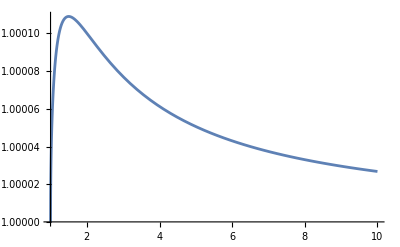

```mathematica
(x^3 E2[x])/((x^3+2 (-2 G M+x) ζ^2) E2[x]-2 ζ √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/.E2[x]->I  x/.G->1/.M->1/.ζ->10^-4//FullSimplify
Plot[%,{x,1,10},PlotRange->All]
```

```mathematica
NxValue=Nx[x]->(Nx[x]/.NxRule//TrigToExp//Expand)/.Exp[Times[a___]K2[x]/x]:>ξ^(a/(2I ζ))/.solveK2/.stationaryN//FullSimplify[#,ζ>0&&E2[x]>0&&G>0]&
```

{Nx[x]→-(ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/(x E2[x]^2),Nx[x]→(ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/(x E2[x]^2)}

```mathematica
Ds2=-NN[x]^2 Dt^2+E2[x]^2/E1[x](Dx+Nx[x] Dt)^2;
gmetric=CoefficientArrays[Ds2,{Dt,Dx},"Symmetric"->True]//Last//Normal;
(gmetric=gmetric/.arealGF/.stationaryN/.Last[NxValue])//MatrixForm
```

(-(x^2 C[1]^2)/E2[x]^2-(C[1]^2 (-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/(x^4 E2[x]^2) | (ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/x^3
(ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/x^3 | E2[x]^2/x^2)

```mathematica
sChGauge=Solve[0==gmetric[[1,2]]^2//FullSimplify,E2[x]]//FullSimplify[#,x>0]&
MatrixForm/@(gmetric/.sChGauge/.C[1]->1//FullSimplify//ExpandAll)
```

{{E2[x]→-x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2)))},{E2[x]→x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2)))}}

{(-1+(2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2 | 0
0 | x^4/(-2 G M x^3+x^4+4 G^2 M^2 ζ^2-4 G M x ζ^2+x^2 ζ^2)),(-1+(2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2 | 0
0 | x^4/(-2 G M x^3+x^4+4 G^2 M^2 ζ^2-4 G M x ζ^2+x^2 ζ^2))}

```mathematica
(PGgauge=gmetric/.E2[x]-> x/.C[1]->1)//FullSimplify//ExpandAll;
(PGgauge=PGgauge/.Times[I,a__]:>√(-Times[a]^2)//ExpandAll)//MatrixForm
```

(-1+(2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2 | √((2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2)
√((2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2) | 1)

```mathematica
PGgauge==(-Dt^2+(Dx+√((2G M)/x-ζ^2/x^2((2G M)/x-1)^2)Dt)^2//CoefficientArrays[#,{Dt,Dx},"Symmetric"->True]&//Last//Normal)//FullSimplify
```

True

## Solve the Hamiltonian Constraint: case 2

```mathematica
Heff2Polymer=Heff2/.polymerRule/.(3 Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E2[x])/(4 G ζ^2)->(3 (1-2 Sin[(ζ K2[x])/(√E1[x])]^2) √E1[x] E2[x])/(4 G ζ^2)//Expand
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+E1'[x]^2/(16 G √E1[x] E2[x])+(Cos[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(16 G √E1[x] E2[x])-(ζ K1[x] Sin[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(8 G E2[x]^2)+(ζ K2[x] Sin[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(8 G E1[x] E2[x])-(√E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)-(Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)+(√E1[x] E1''[x])/(4 G E2[x])+(Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E1''[x])/(4 G E2[x])

```mathematica
mu2Polymer=mu2/.sRule/.polymerRule
```

Cos[(ζ K2[x])/(√E1[x])]^2+(ζ^2 Cos[(ζ K2[x])/(√E1[x])]^2 E1'[x]^2)/(4 E1[x] E2[x]^2)

```mathematica
NxRule=poissonFun[{FF[x](E1[x]-x^2),NN[x]Heff2Polymer+Nx[x] HvGau},canonicalPairs]==0;
NxRule=Solve[NxRule,Nx[x]]//First//FullSimplify;
NxRule=NxRule/.arealGF//Refine[#,x>0]&
```

{Nx[x]→-((4 x^2 ζ^2+4 x^2 E2[x]^2) NN[x] Sin[(2 ζ K2[x])/x])/(8 x ζ E2[x]^2)}

```mathematica
Heff2ArealGF=Heff2Polymer/.arealGF//Refine[#,x>0]&
```

(3 x)/(4 G E2[x])+(3 x Cos[(2 ζ K2[x])/x])/(4 G E2[x])-E2[x]/(2 G x)-(3 x E2[x] Sin[(ζ K2[x])/x]^2)/(2 G ζ^2)+(ζ K2[x] Sin[(2 ζ K2[x])/x])/(2 G E2[x])+(E2[x] K2[x] Sin[(2 ζ K2[x])/x])/(2 G ζ)-(x^2 E2'[x])/(2 G E2[x]^2)-(x^2 Cos[(2 ζ K2[x])/x] E2'[x])/(2 G E2[x]^2)-(x ζ Sin[(2 ζ K2[x])/x] K2'[x])/(2 G E2[x])-(x E2[x] Sin[(2 ζ K2[x])/x] K2'[x])/(2 G ζ)

```mathematica
stationaryN=poissonFun[{FF[x]E2[x],NN[x]Heff2ArealGF},canonicalPairs]//Expand//FullSimplify
stationaryN=DSolve[stationaryN==0,NN[x],x]//First
```

-((ζ^2+E2[x]^2) FF[x] Sin[(2 ζ K2[x])/x] (x NN[x] E2'[x]+E2[x] (-NN[x]+x NN'[x])))/(2 ζ E2[x]^2)

{NN[x]→(x C[1])/E2[x]}

```mathematica
solveK2=-x/E2[x] Heff2ArealGF//Expand//Integrate[#,x]&//Expand
solveK2=(solveK2-M)/. Cos[z_]^2:>1/2 Cos[2z]+1/2//Expand
solveK2=Solve[solveK2==0,Cos[(2ζ K2[x])/x]]//First
```

x/(2 G)+x^3/(4 G ζ^2)-(x^3 Cos[(2 ζ K2[x])/x])/(4 G ζ^2)-(x^3 Cos[(ζ K2[x])/x]^2)/(2 G E2[x]^2)

-M+x/(2 G)+x^3/(4 G ζ^2)-(x^3 Cos[(2 ζ K2[x])/x])/(4 G ζ^2)-x^3/(4 G E2[x]^2)-(x^3 Cos[(2 ζ K2[x])/x])/(4 G E2[x]^2)

{Cos[(2 ζ K2[x])/x]→(-x^3 ζ^2+x^3 E2[x]^2-4 G M ζ^2 E2[x]^2+2 x ζ^2 E2[x]^2)/(x^3 (ζ^2+E2[x]^2))}

```mathematica
NxValue=Nx[x]->(Nx[x]/.NxRule/.Sin[a_]:>-√(1-Cos[a]^2)/.solveK2)/.stationaryN//FullSimplify[#,ζ>0&&E2[x]>0&&x>0]&
```

Nx[x]→(C[1] √((x^3+(-2 G M+x) ζ^2) (x^3+(2 G M-x) E2[x]^2)))/(x E2[x]^2)

```mathematica
mu2PolymerGF=(mu2Polymer/.arealGF//Simplify[#,x>0]&)/. Cos[z_]^2:>1/2 Cos[2z]+1/2/.solveK2//FullSimplify
```

1+((-2 G M+x) ζ^2)/x^3

```mathematica
Ds2=-NN[x]^2 Dt^2+E2[x]^2/(mu2PolymerGF  E1[x])(Dx+Nx[x] Dt)^2;
gmetric=CoefficientArrays[Ds2,{Dt,Dx},"Symmetric"->True]//Last//Normal;
(gmetric=(gmetric/.arealGF/.stationaryN/.NxValue//FullSimplify[#,ζ>0&&E2[x]>0&&x>0]&)/.a_/(√b_):>√(a^2/b//FullSimplify))//MatrixForm
```

(-((-2 G M+x) C[1]^2)/x | (C[1] √((x^3+(-2 G M+x) ζ^2) (x^3+(2 G M-x) E2[x]^2)))/(x^3+(-2 G M+x) ζ^2)
(C[1] √((x^3+(-2 G M+x) ζ^2) (x^3+(2 G M-x) E2[x]^2)))/(x^3+(-2 G M+x) ζ^2) | (x E2[x]^2)/(x^3+(-2 G M+x) ζ^2))

```mathematica
schGauge=Solve[0==gmetric[[1,2]]^2//FullSimplify,E2[x]]//FullSimplify[#,x>0]&
schGauge=(gmetric/.schGauge/.C[1]->1//FullSimplify);
MatrixForm/@sChGauge
```

{{E2[x]→-x^(3/2)/(√(-2 G M+x))},{E2[x]→x^(3/2)/(√(-2 G M+x))}}

{(E2[x]→-x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2)))),(E2[x]→x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2))))}

```mathematica
(PGgauge=gmetric/.E2[x]-> x/.C[1]->1)//FullSimplify//ExpandAll;
(PGgauge=(PGgauge//FullSimplify[#,ζ>0&&G>0&&M>0&&x>0]&))//MatrixForm
```

(-1+(2 G M)/x | (√2 G M x)/(√(G M (x^3+(-2 G M+x) ζ^2)))
(√2 G M x)/(√(G M (x^3+(-2 G M+x) ζ^2))) | x^3/(x^3+(-2 G M+x) ζ^2))

```mathematica
({Dt,Dx}.PGgauge.{Dt,Dx}+Dt^2-(1+ζ^2/x^2-(2G M ζ^2)/x^3)^-1(Dx+√((2G M)/x(1+ζ^2/x^2-(2G M ζ^2)/x^3))Dt)^2//FullSimplify[#,x>0&&M>0&&(x^3+(-2 M+x) ζ^2)>0&&G>0]&)/.a_/(√b_):>√(a^2/b//FullSimplify)
```

0

```mathematica
transM={{a,b},{0,1}};
```

```mathematica
transedMetric=Transpose[transM].PGgauge.transM//FullSimplify;
equs=transedMetric-schGauge[[1]]//Flatten;
solb=Solve[equs[[-1]]==0,b]//FullSimplify
sola=Solve[equs[[1]]==0,a]//FullSimplify
equs[[2]]/.sola/.solb//FullSimplify
```

{{b→-(√2 G M x^2)/((2 G M-x) √(G M (x^3+(-2 G M+x) ζ^2)))},{b→-(√2 G M x^2)/((2 G M-x) √(G M (x^3+(-2 G M+x) ζ^2)))}}

{{a→-1},{a→1}}

{{0,0},{0,0}}

```mathematica
transMP={{a,1},{Derivative[1][R][T],0}};
(metricHom=(Transpose[transMP].PGgauge.transMP//FullSimplify)/.x->R[T])//MatrixForm;
solaa=Solve[metricHom[[1,2]]==0,a]//FullSimplify//First;
metricHom[[1,1]]/.solaa//FullSimplify;
%/.R'[T]->-R[T]^3/(ζ^2+3 R[T]^2 Sin[T]^2)((2 ζ √(2 G M-R[T]) √(1+(ζ^2 (-2 G M+R[T]))/R[T]^3))/R[T]^(3/2))//FullSimplify
%%/.R'[T]->-(2 R[T]^3 Sin[T]Cos[T])/(ζ^2+3 R[T]^2 Sin[T]^2)//FullSimplify
%/.Sin[2T]^2->-(4 ζ^2 (2 G M-R[T]) (2 G M ζ^2-R[T] (ζ^2+R[T]^2)))/R[T]^6//FullSimplify
```

-(4 ζ^2 R[T]^4)/((ζ^2+3 R[T]^2 Sin[T]^2)^2)

(R[T]^10 Sin[2 T]^2)/((-2 G M+R[T]) (-2 G M ζ^2+ζ^2 R[T]+R[T]^3) (ζ^2+3 R[T]^2 Sin[T]^2)^2)

-(4 ζ^2 R[T]^4)/((ζ^2+3 R[T]^2 Sin[T]^2)^2)

## Homogeneous solution of the second spacetime

```mathematica
Heff2Hom=Heff2Polymer/.Derivative[_][_][x]:>0
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)

```mathematica
Meff2Hom=Meff2/.sRule/.polymerRule/.Derivative[_][_][x]:>0
```

(√E1[x])/(2 G)+(E1[x]^(3/2) Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)

```mathematica
homGauge=E1[x]->t^2
dotE1=poissonFun[{E1[x],Heff2Hom NN[x]},canonicalPairs]//FullSimplify
dotE1=dotE1/.homGauge//Simplify[#,t>0]&;
meffGauge=Meff2Hom-M/.homGauge//Simplify[#,t>0]&;
variable=Cases[meffGauge,_Sin,Infinity]//First;
meffGauge=Solve[meffGauge==0,variable]
dotE1=dotE1/.Sin[x_]:>2Sin[x/2] √(1-Sin[x/2]^2)/.meffGauge;
equs=dotE1==2 t//Thread
solNN=Solve[#,NN[x]]&/@equs//FullSimplify//Flatten[#,1]&
NNK2Rule=Flatten/@({meffGauge,solNN}//Transpose)
```

E1[x]→t^2

(E1[x] NN[x] Sin[(2 ζ K2[x])/(√E1[x])])/ζ

{{Sin[(ζ K2[x])/t]→-(√(2 G M-t) ζ)/t^(3/2)},{Sin[(ζ K2[x])/t]→(√(2 G M-t) ζ)/t^(3/2)}}

{-2 √(2 G M-t) √t √(1-((2 G M-t) ζ^2)/t^3) NN[x]==2 t,2 √(2 G M-t) √t √(1-((2 G M-t) ζ^2)/t^3) NN[x]==2 t}

{{NN[x]→-(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))},{NN[x]→(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))}}

{{Sin[(ζ K2[x])/t]→-(√(2 G M-t) ζ)/t^(3/2),NN[x]→-(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))},{Sin[(ζ K2[x])/t]→(√(2 G M-t) ζ)/t^(3/2),NN[x]→(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))}}

```mathematica
dotE2=poissonFun[{E2[x],Heff2Hom NN[x]},canonicalPairs]//FullSimplify;
dotE2=dotE2/.homGauge//Simplify[#,t>0]&
constraint=Heff2Hom/.homGauge//Simplify[#,t>0]&;
constraint=Solve[constraint==0,K1[x]]//First
dotE2=dotE2/.constraint/.NNK2Rule//FullSimplify
dotE2=dotE2/.Sin[2x_]:>2Sin[x] √(1-Sin[x]^2)/.Cot[x_]:>(1-2 Sin[x/2]^2)/(2Sin[x/2] √(1-Sin[x/2]^2))/.Csc[x_]:>HoldForm[1/Sin[x]];
dotE2=MapThread[#1/.#2&,{dotE2,meffGauge}]//ReleaseHold//FullSimplify//DeleteDuplicates
Integrate[#/E2[x],t]&/@dotE2
```

NN[x] (t Cos[(2 ζ K2[x])/t] K1[x]+E2[x] (-(Cos[(2 ζ K2[x])/t] K2[x])/t+Sin[(2 ζ K2[x])/t]/ζ))

{K1[x]→-(E2[x] (ζ^2 Csc[(2 ζ K2[x])/t]-t ζ K2[x]+3 t^2 Csc[(2 ζ K2[x])/t] Sin[(ζ K2[x])/t]^2))/(t^3 ζ)}

{(E2[x] (2 (3 G M-t) ζ^2 Cot[(2 ζ K2[x])/t]-t^3 Sin[(2 ζ K2[x])/t]))/(√(2 G M-t) t^(5/2) ζ √(1+((-2 G M+t) ζ^2)/t^3)),(E2[x] (2 (-3 G M+t) ζ^2 Cot[(2 ζ K2[x])/t]+t^3 Sin[(2 ζ K2[x])/t]))/(√(2 G M-t) t^(5/2) ζ √(1+((-2 G M+t) ζ^2)/t^3))}

{((t^3 (-G M+t)+2 G M (-2 G M+t) ζ^2) E2[x])/(t (-2 G M+t) (t^3+(-2 G M+t) ζ^2))}

{-Log[t]+1/2 Log[-2 G M+t]+1/2 Log[t^3-2 G M ζ^2+t ζ^2]}

### second Gauge

```mathematica
homGauge2=K2[x]->(√E1[x] t)/ζ;
dotE1=poissonFun[{E1[x],NN[x]Heff2Hom},canonicalPairs]/.homGauge2
meffGauge2=Meff2Hom-M/.homGauge2/.E1[x]->R[t]^2//Simplify[#,R[t]>0]&;
RofT=(Solve[meffGauge2==0,R[t]]//First//FullSimplify[#,Sin[t]>0]&)
RofT/.-9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2)->1/3 β[t]^3//FullSimplify[#,β[t]>0]&
dotR=poissonFun[{√E1[x],NN[x]Heff2Hom},canonicalPairs]/.homGauge2/.E1[x]->R[t]^2//Simplify[#,R[t]>0]&
```

(E1[x] NN[x] Sin[2 t])/ζ

{R[t]→(Csc[t] (-3^(2/3) ζ^2+3^(1/3) (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(2/3)))/(3 (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(1/3))}

{R[t]→(Csc[t] (-3^(2/3) ζ^2+3^(1/3) (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(2/3)))/(3 (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(1/3))}

(Cos[t] NN[x] R[t] Sin[t])/ζ

```mathematica
dotM=(D[meffGauge2,t])//Expand
dolDotR=Solve[dotM==0,R'[t]]//First
Solve[R'[t]==dotR/.dolDotR,NN[x]]
```

(Cos[t] R[t]^3 Sin[t])/(G ζ^2)+R'[t]/(2 G)+(3 R[t]^2 Sin[t]^2 R'[t])/(2 G ζ^2)

{R'[t]→-(2 Cos[t] R[t]^3 Sin[t])/(ζ^2+3 R[t]^2 Sin[t]^2)}

{{NN[x]→-(2 ζ R[t]^2)/(ζ^2+3 R[t]^2 Sin[t]^2)}}

```mathematica
dotE2=poissonFun[{E2[x],Heff2Hom NN[x]},canonicalPairs]//FullSimplify;
K1sol=Solve[Heff2Hom==0,K1[x]]//First;
dotE2=dotE2/.K1sol/.homGauge2/.E1[x]->R[t]^2//Simplify[#,R[t]>0]&//FullSimplify;
NNinDotR=Solve[D[R[t],t]==dotR,NN[x]]//First
dotE2=dotE2/.NNinDotR//FullSimplify
sint=Solve[meffGauge2==0,Sin[t]]//Last
dotE21=dotE2/.t->ArcSin[Sin[t]/.sint]/.{R[_]:>R[t],R'[_]->R'[t]}//FullSimplify
dotE22=dotE2/.t->Pi-ArcSin[Sin[t]/.sint]/.{R[_]:>R[t],R'[_]->R'[t]}//FullSimplify
dotE21-dotE21//FullSimplify
```

{NN[x]→(ζ Csc[t] Sec[t] R'[t])/R[t]}

-(E2[x] Sec[t] (2 ζ^2 Cot[2 t] Csc[t]+(-2+Cos[2 t]) R[t]^2 Sec[t]) R'[t])/(2 R[t]^3)

{Sin[t]→(ζ √(2 G M-R[t]))/R[t]^(3/2)}

(E2[x] (4 G^2 M^2 ζ^2-2 G M ζ^2 R[t]+G M R[t]^3-R[t]^4) R'[t])/((2 G M-R[t]) R[t] (-2 G M ζ^2+ζ^2 R[t]+R[t]^3))

(E2[x] (-4 G^2 M^2 ζ^2+2 G M ζ^2 R[t]-G M R[t]^3+R[t]^4) R'[t])/((2 G M-R[t]) R[t] (2 G M ζ^2-R[t] (ζ^2+R[t]^2)))

0

```mathematica
(dotE21/(E2[x] R'[t])/.R[t]->y//Integrate[#,y]&//Exp)/.y->R[t]
```

(√(-2 G M+R[t]) √(-2 G M ζ^2+ζ^2 R[t]+R[t]^3))/R[t]

## Spacetime Properties: the first model

```mathematica
f1=(2M)/x-ζ^2/x^2(2 M/x-1)^2
```

(2 M)/x-((-1+(2 M)/x)^2 ζ^2)/x^2

```mathematica
(Solve[1-f1==0,x]//FullSimplify[#,α>0]&)/.(-9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))->1/3( β )^3//FullSimplify[#,β>0&&ζ>0]&//Expand
```

{{x→2 M},{x→-β/3+ζ^2/β},{x→-1/3 (-1)^(2/3) β-((-1)^(1/3) ζ^2)/β},{x→1/3 (-1)^(1/3) β+((-1)^(2/3) ζ^2)/β}}

```mathematica
metric1={{-1-f1,0,0,0},{0,(1-f1)^(-1),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
coor={t,x,θ,ϕ};
Racci1=racciCurFromMetric[coor,metric1]//FullSimplify;
G1=Racci1-1/2 metric1 Tr[Racci1.Inverse[metric1]]//FullSimplify;
-G1[[1,1]]/metric1[[1,1]]//FullSimplify
%/.M->0
```

((-6 M+x) (-2 M+x) ζ^2)/x^6

ζ^2/x^4

## Spacetime property: the second property

```mathematica
g00=-(4 ζ^2 R[t]^4)/((ζ^2+3 R[t]^2 Sin[t]^2)^2);
g11=-1+(2 M)/R[t];
```

```mathematica
Rfun=R->Function[t,(Csc[t] (3^(2/3) ζ^2-3^(1/3) (-9 M ζ^2 Sin[t]+√3 √(ζ^6+27 M^2 ζ^4 Sin[t]^2))^(2/3)))/(3 (-9 M ζ^2 Sin[t]+√3 √(ζ^6+27 M^2 ζ^4 Sin[t]^2))^(1/3))];
```

```mathematica
g2={{g00,0,0,0},{0,g11,0,0},{0,0,R[t]^2,0},{0,0,0,R[t]^2 Sin[θ]^2}};
coor2={t,x,θ,ϕ}
racciScalar=racciCurFromMetric[coor,g2].Inverse[g2]//Tr//Simplify;
racciScalar=racciScalar/.Rfun/.t->Pi/2;
```

{t,x,θ,ϕ}

```mathematica
g2Sch={{-(1-(2M)/x),0,0,0},{0,(1+ζ^2/x^2(1-(2M)/x))^-1(1-(2M)/x)^-1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
coor={t,x,θ,ϕ};
racciScalarSchFun=racciCurFromMetric[coor,g2Sch].Inverse[g2Sch]//Tr//Expand//FullSimplify;
racciScalarSch=(racciScalarSchFun/.Solve[(1+ζ^2/x^2(1-(2M)/x))==0,x]//First//FullSimplify)
```

(162 (9 M ζ^3+√3 ζ √(27 M^2 ζ^4+ζ^6))^2 (9 M^2-(2 ζ^2)/3+ζ^4/(3^(2/3) (9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))+((9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))/(3 3^(1/3))+(7 M (3^(1/3) ζ^2-(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3)))/(3 (3 M ζ^2+√(9 M^2 ζ^4+ζ^6/3))^(1/3))))/((-3^(1/3) ζ^2+(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))^6)

```mathematica
(racciScalar-racciScalarSch)/.{M->SetPrecision[RandomReal[],200],ζ->1}
```

0.

```mathematica
Series[racciScalarSch,{M,Infinity,1}]//Simplify[#,M>0&&ζ>0]&
{racciScalarSch,Normal[%]}/.{M->RandomReal[{1000,10000}],ζ->1.}
```

9/(2 ζ^2)+(2^(1/3) (1/M)^(2/3))/ζ^(4/3)+O[1/M]^(4/3)

{4.50281,4.50281}

```mathematica
racciScalarSchFun/.x->2M
```

-ζ^2/(32 M^4)

```mathematica
invg2Sch=Inverse[g2Sch]//Simplify;
```

```mathematica
riemann=riemannTensorFromMetric[coor,g2Sch];
```

```mathematica
Kretschmann=Sum[riemann[[a,b,c,d]]riemann[[ap,bp,cp,dp]]invg2Sch[[a,ap]]invg2Sch[[b,bp]]invg2Sch[[c,cp]]g2Sch[[d,dp]],{a,1,4},{b,1,4},{c,1,4},{d,1,4},{ap,1,4},{bp,1,4},{cp,1,4},{dp,1,4}]//Simplify
```

(4 (201 M^4 ζ^4+3 x^4 ζ^4-8 M x^3 ζ^2 (x^2+4 ζ^2)-2 M^3 (42 x^3 ζ^2+137 x ζ^4)+M^2 (12 x^6+56 x^4 ζ^2+139 x^2 ζ^4)))/x^12

```mathematica
Kretschmann/.Solve[(1+ζ^2/x^2(1-(2M)/x))==0,x]//First//Simplify//Series[#,{M,Infinity,1}]&//Simplify[#,M>0&&ζ>0]&
```

81/(4 ζ^4)+(9 2^(1/3) (1/M)^(2/3))/ζ^(10/3)+O[1/M]^(4/3)

```mathematica
Plot[Kretschmann/.{ζ->1,M->1000},{x,0.1,1}]
```

-Graphics-

## Check the spacetime

```mathematica
g2Sch={{-(1-(2M)/x),0,0,0},{0,(1+ζ^2/x^2(1-(2M)/x))^-1(1-(2M)/x)^-1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
g2Schp={{-(1-(2M)/x),0,0,0},{0,(1-(2ζ M)/x)^-1(1-(2M)/x)^-1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
coor={t,x,θ,ϕ};
```

```mathematica
R2=racciCurFromMetric[coor,g2Sch].Inverse[g2Sch]//Tr//Expand//FullSimplify
R2p=racciCurFromMetric[coor,g2Schp].Inverse[g2Schp]//Tr//Expand//Simplify
```

(2 (9 M^2-7 M x+x^2) ζ^2)/x^6

(6 M^2 ζ)/x^4

```mathematica
(R2/.Solve[(1+ζ^2/x^2(1-(2M)/x))==0,x]//First//FullSimplify)
Limit[%,M->Infinity]//FullSimplify[#,M>0&ζ>0]&
Series[%%,{M,Infinity,1}]//FullSimplify[#,M>0&ζ>0]&
```

(162 (9 M ζ^3+√3 ζ √(27 M^2 ζ^4+ζ^6))^2 (9 M^2-(2 ζ^2)/3+ζ^4/(3^(2/3) (9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))+((9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))/(3 3^(1/3))+(7 M (3^(1/3) ζ^2-(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3)))/(3 (3 M ζ^2+√(9 M^2 ζ^4+ζ^6/3))^(1/3))))/((-3^(1/3) ζ^2+(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))^6)

9/(2 ζ^2)

9/(2 ζ^2)+(2^(1/3) (1/M)^(2/3))/Abs[ζ]^(4/3)+O[1/M]^(4/3)

```mathematica
Ds2=-Dt^2 NN[x]^2+(E2[x]^2 (Dx+Dt Nx[x])^2)/(μ E1[x])+ E1[x](Dθ^2+Sin[θ]^2 Dϕ^2)
CoefficientArrays[Ds2,{Dt,Dx,Dθ,Dϕ},"Symmetric"->True]//Last//Normal//Inverse//FullSimplify//MatrixForm
```

-Dt^2 NN[x]^2+(E2[x]^2 (Dx+Dt Nx[x])^2)/(μ E1[x])+E1[x] (Dθ^2+Dϕ^2 Sin[θ]^2)

(-1/NN[x]^2 | Nx[x]/NN[x]^2 | 0 | 0
Nx[x]/NN[x]^2 | (μ E1[x])/E2[x]^2-Nx[x]^2/NN[x]^2 | 0 | 0
0 | 0 | 1/E1[x] | 0
0 | 0 | 0 | Csc[θ]^2/E1[x])

## Matter coupling

```mathematica
canonicalPairsMatter={{{K1[x],E1[x]},2 G},{{K2[x],E2[x]},G},{{T[x],Pt[x]},1}};
```

```mathematica
HvMatter=Pt[x] T'[x]
```

Pt[x] T'[x]

```mathematica
dustTimeGauge=D[T[x],x]->0;
```

### classical theory

```mathematica
Hmatter=√(Pt[x]^2+E1[x]/E2[x]^2 Pt[x]^2 D[T[x],x]^2)
```

√(Pt[x]^2+(E1[x] Pt[x]^2 T'[x]^2)/E2[x]^2)

```mathematica
HtotalCl=HScal+ Hmatter
Hvtotal=HvGau+HvMatter
```

√(Pt[x]^2+(E1[x] Pt[x]^2 T'[x]^2)/E2[x]^2)+(-8 E1[x] E2[x]^2 K1[x] K2[x]-4 E2[x]^3 (1+K2[x]^2)-4 E1[x] E1'[x] E2'[x]+E2[x] (E1'[x]^2+4 E1[x] E1''[x]))/(8 G √E1[x] E2[x]^2)

-(K1[x] E1'[x]-2 E2[x] K2'[x])/(2 G)+Pt[x] T'[x]

```mathematica
(poissonFun[{Nx1[x]Hvtotal,Nx2[x]Hvtotal},canonicalPairsMatter]//Expand)//FullSimplify
%==-(Nx2[x] Nx1'[x]-Nx1[x] Nx2'[x])Hvtotal//FullSimplify
```

((Nx2[x] Nx1'[x]-Nx1[x] Nx2'[x]) (K1[x] E1'[x]-2 (E2[x] K2'[x]+G Pt[x] T'[x])))/(2 G)

True

```mathematica
poissonHHMatter=(poissonFun[{N1[x]HtotalCl,N2[x]HtotalCl},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand//FullSimplify
poissonHHMatter==-E1[x]/E2[x]^2(N2[x] N1'[x]-N1[x] N2'[x])Hvtotal//FullSimplify
```

(E1[x] (N2[x] N1'[x]-N1[x] N2'[x]) (K1[x] E1'[x]-2 (E2[x] K2'[x]+G Pt[x] T'[x])))/(2 G E2[x]^2)

True

```mathematica
tofixGauge1=(poissonFun[{χ[x]D[T[x],x],Nx[x]Hvtotal+NN[x] HtotalCl},canonicalPairsMatter]//Expand)/.dustTimeGauge//Simplify[#,Pt[x]>0]&
```

-NN[x] χ'[x]

```mathematica
tofixGauge2=(poissonFun[{(E1[x]-x^2),Nx[x]Hvtotal+NN[x]HtotalCl},canonicalPairsMatter]//Expand)
tofixGauge2=tofixGauge2/.Times[a___,χ'[x],b___]:>χ[x]D[Times[a,b],x]/.arealGF//Expand//FullSimplify[#,x>0]&
NxN=DSolve[tofixGauge2==0,Nx[x],x]//First
NxValueMatter=Nx[x]/.NxN/.NN[x]->1
```

2 √E1[x] K2[x] NN[x]+Nx[x] E1'[x]

2 x (K2[x] NN[x]+Nx[x])

{Nx[x]→-K2[x] NN[x]}

-K2[x]

```mathematica
dotE2Matter=poissonFun[{E2[x],HtotalCl+NxValueMatter Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
dotK2Matter=poissonFun[{K2[x],HtotalCl+NxValueMatter Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
```

(K2[x] (E2[x]-x E2'[x]))/x

x/(2 E2[x]^2)-(1+K2[x]^2+2 x K2[x] K2'[x])/(2 x)

```mathematica
barM=Mcl/.sRule/.arealGF//Simplify[#,x>0]&//Expand
```

x/(2 G)-x^3/(2 G E2[x]^2)+(x K2[x]^2)/(2 G)

```mathematica
dotBarM=D[barM,E2[x]]dotE2Matter+D[barM,K2[x]]dotK2Matter//FullSimplify//Expand
dotBarM==-K2[x]D[barM,x]//Expand
```

-K2[x]/(2 G)+(3 x^2 K2[x])/(2 G E2[x]^2)-K2[x]^3/(2 G)-(x^3 K2[x] E2'[x])/(G E2[x]^3)-(x K2[x]^2 K2'[x])/G

True

```mathematica
rho=1/(4Pi x^2)D[barM,x]//Expand
dotRho=D[rho,E2[x]]dotE2Matter+D[rho,K2[x]]dotK2Matter+D[rho,E2'[x]]D[dotE2Matter,x]+D[rho,K2'[x]]D[dotK2Matter,x]//Expand
dotRho==-rho D[K2[x],x]-K2[x]D[rho,x]-2 K2[x]/x rho//Expand
```

1/(8 G π x^2)-3/(8 G π E2[x]^2)+K2[x]^2/(8 G π x^2)+(x E2'[x])/(4 G π E2[x]^3)+(K2[x] K2'[x])/(4 G π x)

(3 K2[x])/(4 G π x E2[x]^2)-(3 K2[x] E2'[x])/(2 G π E2[x]^3)+(3 x K2[x] E2'[x]^2)/(4 G π E2[x]^4)-K2'[x]/(8 G π x^2)+(3 K2'[x])/(8 G π E2[x]^2)-(5 K2[x]^2 K2'[x])/(8 G π x^2)-(x E2'[x] K2'[x])/(4 G π E2[x]^3)-(K2[x] K2'[x]^2)/(2 G π x)-(x K2[x] E2''[x])/(4 G π E2[x]^3)-(K2[x]^2 K2''[x])/(4 G π x)

True

```mathematica
solK2=DSolve[D[2 K2[x]/x+D[K2[x],x],x]==0,K2[x],x]//First
```

{K2[x]→C[1]/x^2+x C[2]}

```mathematica
epsol=Solve[(4Pi ρ)/3 x^3+C[3]==x/(2 G)(K2[x]^2-ep)/.solK2,ep]//FullSimplify//First
```

{ep→(3 (C[1]+x^3 C[2])^2-2 G (4 π x^6 ρ+3 x^3 C[3]))/(3 x^4)}

```mathematica
-(K2[x]/.solK2)D[ep/.epsol,x]//FullSimplify//Expand
(1/(2 x)ep/.epsol)-1/(2x)D[x K2[x]^2/.solK2,x]//FullSimplify
%%/.{C[1]->0,C[3]->0}//FullSimplify
%%/.{C[1]->0,C[3]->0}//FullSimplify
```

(16 G π ρ C[1])/(3 x)+(4 C[1]^3)/x^7+16/3 G π x^2 ρ C[2]+(6 C[1]^2 C[2])/x^4-2 x^2 C[2]^3-(2 G C[1] C[3])/x^4-(2 G C[2] C[3])/x

-4/3 G π x ρ+(2 C[1]^2)/x^5+(C[1] C[2])/x^2-x C[2]^2-(G C[3])/x^2

2/3 x^2 C[2] (8 G π ρ-3 C[2]^2)

-1/3 x (4 G π ρ+3 C[2]^2)

### effective model 1

```mathematica
HmatterEff1=√(Pt[x]^2+E1[x]/E2[x]^2 Pt[x]^2 D[T[x],x]^2)
```

√(Pt[x]^2+(E1[x] Pt[x]^2 T'[x]^2)/E2[x]^2)

```mathematica
HtotalEff1=Heff1Polymer+HmatterEff1
Hvtotal=HvGau+HvMatter
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) E1'[x]^2)/(8 G √E1[x] E2[x])+(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ K1[x] E1'[x]^2)/(4 G E2[x]^2)-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ K2[x] E1'[x]^2)/(4 G E1[x] E2[x])-(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+√(Pt[x]^2+(E1[x] Pt[x]^2 T'[x]^2)/E2[x]^2)+(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) √E1[x] E1''[x])/(2 G E2[x])

-(K1[x] E1'[x]-2 E2[x] K2'[x])/(2 G)+Pt[x] T'[x]

```mathematica
poissonHHMatter=(poissonFun[{N1[x]HtotalEff1,N2[x]HtotalEff1},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand//FullSimplify
poissonHHMatter==-E1[x]/E2[x]^2(N2[x] N1'[x]-N1[x] N2'[x])Hvtotal//FullSimplify
```

(E1[x] (N2[x] N1'[x]-N1[x] N2'[x]) (K1[x] E1'[x]-2 (E2[x] K2'[x]+G Pt[x] T'[x])))/(2 G E2[x]^2)

True

```mathematica
tofixGauge1=(poissonFun[{χ[x]D[T[x],x],Nx[x]Hvtotal+NN[x] HtotalEff1},canonicalPairsMatter]//Expand)/.dustTimeGauge//Simplify[#,Pt[x]>0]&
```

-NN[x] χ'[x]

```mathematica
tofixGauge2=(poissonFun[{(E1[x]-x^2),Nx[x]Hvtotal+NN[x]HtotalEff1},canonicalPairsMatter]//Expand)
tofixGauge2=tofixGauge2/.Times[a___,χ'[x],b___]:>χ[x]D[Times[a,b],x]/.arealGF//Expand//FullSimplify[#,x>0]&
NxN=DSolve[tofixGauge2==0,Nx[x],x]//FullSimplify//First
NxValueMatter=Nx[x]/.NxN/.NN[x]->1
```

(E1[x] NN[x] Sin[(2 ζ K2[x])/(√E1[x])])/ζ+Nx[x] E1'[x]-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ NN[x] E1'[x]^2)/(2 E2[x]^2)

x (-(2 ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ NN[x])/E2[x]^2+2 Nx[x]+(x NN[x] Sin[(2 ζ K2[x])/x])/ζ)

{Nx[x]→(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ NN[x])/E2[x]^2-(x NN[x] Sin[(2 ζ K2[x])/x])/(2 ζ)}

(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ)/E2[x]^2-(x Sin[(2 ζ K2[x])/x])/(2 ζ)

```mathematica
hPhysical=HtotalEff1+NxValueMatter Hvtotal/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&//Expand
```

(3 ⅇ^((2 ⅈ ζ K2[x])/x) x)/(2 G E2[x])-E2[x]/(2 G x)-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) ζ K2[x])/(G E2[x])+√(Pt[x]^2)-(3 x E2[x] Sin[(ζ K2[x])/x]^2)/(2 G ζ^2)+(E2[x] K2[x] Sin[(2 ζ K2[x])/x])/(2 G ζ)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^2 E2'[x])/(G E2[x]^2)+(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ K2'[x])/(G E2[x])-(x E2[x] Sin[(2 ζ K2[x])/x] K2'[x])/(2 G ζ)

```mathematica
dotE2MatterEff=poissonFun[{E2[x],HtotalEff1+NxValueMatter Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
dotK2MatterEff=poissonFun[{K2[x],HtotalEff1+NxValueMatter Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
```

((-2 ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) ζ^2+E2[x]^2 Sin[(2 ζ K2[x])/x]) (E2[x]-x E2'[x]))/(2 ζ E2[x]^2)

1/2 (-1/x+(ⅇ^((2 ⅈ ζ K2[x])/x) (x-2 ⅈ ζ K2[x]+2 ⅈ x ζ K2'[x]))/E2[x]^2+(-3 x Sin[(ζ K2[x])/x]^2+ζ Sin[(2 ζ K2[x])/x] (K2[x]-x K2'[x]))/ζ^2)

```mathematica
dotE2MatterEff==NxValueMatter/x(D[E2[x],x]x-E2[x]) //FullSimplify
dotK2MatterEff==-1/(2x)-1/(2x)D[x^3/ζ^2 Sin[(ζ K2[x])/x]^2,x]+x/(2 E2[x]^2)D[x Exp[(2 I ζ K2[x])/x],x]//FullSimplify
```

True

True

### Effective model 2

```mathematica
mu2sRule=mu2/.sRule
```

Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2+(Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2 λ[E1[x]]^2 E1'[x]^2)/(4 E2[x]^2)

```mathematica
HmatterEff2=√(Pt[x]^2(1+mu2sRule E1[x]/E2[x]^2 D[T[x],x]^2))/.sRule//FullSimplify
```

√(Pt[x]^2 (1+(Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2 E1[x] (4 E2[x]^2+λ[E1[x]]^2 E1'[x]^2) T'[x]^2)/(4 E2[x]^4)))

```mathematica
HtotalEff2=Heff2+HmatterEff2
Hvtotal=HvGau+HvMatter
```

-E2[x]/(2 G √E1[x])-E2[x]/(4 G √E1[x] λ[E1[x]]^2)+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E2[x])/(4 G √E1[x] λ[E1[x]]^2)-(√E1[x] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])])/(2 G λ[E1[x]])+E1'[x]^2/(16 G √E1[x] E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E1'[x]^2)/(16 G √E1[x] E2[x])-(√E1[x] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ[E1[x]] E1'[x]^2)/(8 G E2[x]^2)-(√E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)+√(Pt[x]^2 (1+(Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2 E1[x] (4 E2[x]^2+λ[E1[x]]^2 E1'[x]^2) T'[x]^2)/(4 E2[x]^4)))+(√E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^3)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]]^3)-(√E1[x] E2[x] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] E2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E1'[x]^2 λ'[E1[x]])/(4 G E2[x])-(√E1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] E1'[x]^2 λ'[E1[x]])/(4 G E2[x])-(√E1[x] E2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ'[E1[x]])/(G λ[E1[x]])-(√E1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ[E1[x]] E1'[x]^2 ψ'[E1[x]])/(4 G E2[x])+(√E1[x] E1''[x])/(4 G E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E1''[x])/(4 G E2[x])

-(K1[x] E1'[x]-2 E2[x] K2'[x])/(2 G)+Pt[x] T'[x]

```mathematica
poissonHHMatter2=(poissonFun[{N1[x]HtotalEff2,N2[x]HtotalEff2},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand//FullSimplify
poissonHHMatter2==-mu2sRule E1[x]/E2[x]^2(N2[x] N1'[x]-N1[x] N2'[x])Hvtotal//FullSimplify
```

-(Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2 E1[x] (4 E2[x]^2+λ[E1[x]]^2 E1'[x]^2) (N2[x] N1'[x]-N1[x] N2'[x]) (-K1[x] E1'[x]+2 E2[x] K2'[x]+2 G Pt[x] T'[x]))/(8 G E2[x]^4)

True

```mathematica
Meff2sRule=Meff2/.sRule
```

(√E1[x])/(2 G)+(√E1[x] Sin[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2)/(2 G λ[E1[x]]^2)-(Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2 √E1[x] E1'[x]^2)/(8 G E2[x]^2)

```mathematica
poiMHx=(poissonFun[{χ[x]Meff2sRule,Nx[x]Hvtotal},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[1][χ][x]]:>-D[Times[a],x]χ[x]/.χ[x]->1;
poiMHx==Nx[x] D[Meff2sRule,x]//FullSimplify
```

True

```mathematica
deltaM=(poissonFun[{χ[x]Meff2sRule,λ[x]NN[x] HtotalEff2},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[1][χ][x]]:>-D[Times[a],x]χ[x]/.χ[x]->1//Simplify;
lieM=(poissonFun[{χ[x]Meff2sRule,NN[x] HtotalEff2},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[1][χ][x]]:>-D[Times[a],x]χ[x]/.χ[x]->1//Simplify;
deltaM==λ[x]lieM
```

True

```mathematica
HtotalEff2Polymer=HtotalEff2/.λ->Function[x,ζ/(√x)]/.ψ->Function[x,0]
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x])/(4 G ζ^2)+(3 Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E2[x])/(4 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+E1'[x]^2/(16 G √E1[x] E2[x])+(Cos[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(16 G √E1[x] E2[x])-(ζ K1[x] Sin[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(8 G E2[x]^2)+(ζ K2[x] Sin[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(8 G E1[x] E2[x])-(√E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)-(Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)+√(Pt[x]^2 (1+(Cos[(ζ K2[x])/(√E1[x])]^2 E1[x] (4 E2[x]^2+(ζ^2 E1'[x]^2)/E1[x]) T'[x]^2)/(4 E2[x]^4)))+(√E1[x] E1''[x])/(4 G E2[x])+(Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E1''[x])/(4 G E2[x])

```mathematica
NxValueMatter2=poissonFun[{E1[x]-x^2,NN[x] HtotalEff2Polymer+Nx[x]Hvtotal},canonicalPairsMatter]//FullSimplify;
NxValueMatter2=Nx[x]/.Solve[NxValueMatter2==0,Nx[x]]//First;
NxValueMatter2=NxValueMatter2/.NN[x]->1/.arealGF//FullSimplify[#,x>0]&
```

-(x (ζ^2+E2[x]^2) Sin[(2 ζ K2[x])/x])/(2 ζ E2[x]^2)

```mathematica
Meff2ArealGF=Meff2sRule/.polymerRule/.arealGF//FullSimplify[#,x>0]&//Expand
```

x/(2 G)-(x^3 Cos[(ζ K2[x])/x]^2)/(2 G E2[x]^2)+(x^3 Sin[(ζ K2[x])/x]^2)/(2 G ζ^2)

```mathematica
dotE2MatterEff2=poissonFun[{E2[x],HtotalEff2Polymer+NxValueMatter2 Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
dotK2MatterEff2=poissonFun[{K2[x],HtotalEff2Polymer+NxValueMatter2 Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
dotE2MatterEff2==-NxValueMatter2/x(E2[x]-x E2'[x])//FullSimplify
dotK2MatterEff2==-1/(2x)-1/(2x)D[x^3/ζ^2 Sin[(ζ K2[x])/x]^2,x]+x/(2 E2[x]^2)D[x Cos[(ζ K2[x])/x]^2,x]//FullSimplify
```

((ζ^2+E2[x]^2) Sin[(2 ζ K2[x])/x] (E2[x]-x E2'[x]))/(2 ζ E2[x]^2)

(x^2 ζ^2-3 x^2 E2[x]^2-2 ζ^2 E2[x]^2+x^2 Cos[(2 ζ K2[x])/x] (ζ^2+3 E2[x]^2)+2 x ζ (ζ^2+E2[x]^2) Sin[(2 ζ K2[x])/x] (K2[x]-x K2'[x]))/(4 x ζ^2 E2[x]^2)

True

True

### Effective model 3

```mathematica
polymerRule3={λ->Function[s1,ζ^2/s1],ψ->Function[x,0]}
```

{λ→Function[s1,ζ^2/s1],ψ→Function[x,0]}

```mathematica
mu3sRule=mu3/.sRule
```

Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]^2

```mathematica
HmatterEff3=√(Pt[x]^2+mu3sRule E1[x]/E2[x]^2 Pt[x]^2 D[T[x],x]^2)
```

√(Pt[x]^2+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]^2 E1[x] Pt[x]^2 T'[x]^2)/E2[x]^2)

```mathematica
HtotalEff3=Heff3+HmatterEff3
Hvtotal=HvGau+HvMatter
```

-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] K1[x] K2[x])/G-(E2[x] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))])/(2 G √E1[x] λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+√(Pt[x]^2+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]^2 E1[x] Pt[x]^2 T'[x]^2)/E2[x]^2)+(√E1[x] E2[x] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] λ'[E1[x]])/(G λ[E1[x]]^2)-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] λ'[E1[x]])/(G λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] K2[x]^2 λ'[E1[x]])/(G λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]])+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E1'[x]^2 λ'[E1[x]])/(4 G E2[x] λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] ψ'[E1[x]])/G+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E1''[x])/(2 G E2[x])

-(K1[x] E1'[x]-2 E2[x] K2'[x])/(2 G)+Pt[x] T'[x]

```mathematica
poissonHHMatter3=(poissonFun[{N1[x]HtotalEff3,N2[x]HtotalEff3},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand//FullSimplify
poissonHHMatter3==-mu3sRule E1[x]/E2[x]^2(N2[x] N1'[x]-N1[x] N2'[x])Hvtotal//FullSimplify
```

(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]^2 E1[x] (N2[x] N1'[x]-N1[x] N2'[x]) (K1[x] E1'[x]-2 (E2[x] K2'[x]+G Pt[x] T'[x])))/(2 G E2[x]^2)

True

```mathematica
Meff3sRule=Meff3/.sRule
```

(√E1[x] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))])/(2 G λ[E1[x]])

```mathematica
poiMHx=(poissonFun[{χ[x]Meff3sRule,Nx[x]Hvtotal},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[1][χ][x]]:>-D[Times[a],x]χ[x]/.χ[x]->1;
poiMHx==Nx[x] D[Meff3sRule,x]//FullSimplify
```

True

```mathematica
deltaM=(poissonFun[{χ[x]Meff3sRule,λ[x]NN[x] HtotalEff3},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[1][χ][x]]:>-D[Times[a],x]χ[x]/.χ[x]->1//Simplify;
lieM=(poissonFun[{χ[x]Meff3sRule,NN[x] HtotalEff3},canonicalPairsMatter]//Expand)/.Times[a___,Derivative[1][χ][x]]:>-D[Times[a],x]χ[x]/.χ[x]->1//Simplify;
deltaM==λ[x]lieM
```

True

```mathematica
HtotalEff3Polymer=HtotalEff3/.polymerRule3//Simplify//Expand
```

(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] E2[x])/(G √E1[x])-(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] √E1[x] K1[x] K2[x])/G+(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] E2[x] K2[x]^2)/(G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]])/(2 G ζ^2)-(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] E1'[x]^2)/(4 G √E1[x] E2[x])-(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+√(Pt[x]^2 (1+(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]]^2 E1[x] T'[x]^2)/E2[x]^2))+(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] √E1[x] E1''[x])/(2 G E2[x])

```mathematica
tofixGauge1=poissonFun[{λ[x]D[T[x],x],HtotalEff3Polymer NN[x]+Nx[x]Hvtotal},canonicalPairsMatter]/.dustTimeGauge//Simplify[#,Pt[x]>0]&
```

-NN[x] λ'[x]

```mathematica
NxValueMatter3=poissonFun[{E1[x]-x^2,NN[x] HtotalEff3Polymer +Nx[x]Hvtotal},canonicalPairsMatter]//FullSimplify;
NxValueMatter3=Nx[x]/.Solve[NxValueMatter3==0,Nx[x]]//First;
NxValueMatter3=NxValueMatter3/.NN[x]->1/.arealGF//FullSimplify[#,x>0]&
```

-Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] K2[x]

```mathematica
Meff3ArealGF=Meff3sRule/.polymerRule3/.arealGF//FullSimplify[#,x>0]&//Expand//FullSimplify
```

(x^3 Sin[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2])/(2 G ζ^2)

```mathematica
HtotalEff3Polymer+NxValueMatter3 Hvtotal-√(Pt[x]^2)/.dustTimeGauge/.arealGF//Simplify[#,x>0]&
%==(-E2[x])/x D[Meff3ArealGF,x]//Simplify
```

1/(2 G x E2[x]^2)(-2 x^3 Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] E2'[x]+E2[x]^3 (2 Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2]+2 Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] K2[x]^2-(3 x^2 Sin[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2])/ζ^2-2 x Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] K2[x] K2'[x]))

True

```mathematica
dotE2MatterEff3=poissonFun[{E2[x],HtotalEff3Polymer+NxValueMatter3 Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&
dotK2MatterEff3=poissonFun[{K2[x],HtotalEff3Polymer+NxValueMatter3 Hvtotal},canonicalPairsMatter]/.dustTimeGauge/.arealGF//FullSimplify[#,x>0]&//Expand
dotE2MatterEff3==-NxValueMatter3/x(E2[x]-x E2'[x])//FullSimplify
dotK2MatterEff3==- x/(2 ζ^2) D[ x Sin[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2],x]-(x Sin[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2])/ζ^2+(x^3 Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] D[E2[x]/x,x])/E2[x]^3//FullSimplify
```

(Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] K2[x] (E2[x]-x E2'[x]))/x

Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2]/x-(x Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2])/E2[x]^2+(Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] K2[x]^2)/x-(3 x Sin[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2])/(2 ζ^2)-Cos[(ζ^2 (1-x^2/E2[x]^2+K2[x]^2))/x^2] K2[x] K2'[x]

True

True